```mathematica
n=30;
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
ηv[a_]:=(-1)^(a[[1]]+1);
Nv[a_]:=2(-1)^a[[1]] Cos[(π a[[1]])/4];
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(p'-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[p'], Table[{p'/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];
h = hv @@@ H;
H //Echo[#,"(r,s): "]&;
h //Echo[#,"h = "]&;
s=Outer[sv, H,H,1]//Simplify;
z={
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,2,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1}
};
t=DiagonalMatrix[tv/@H];
```

c =   7/10

(r,s):   {{1,1},{1,2},{1,3},{1,4},{2,1},{2,2}}

h =   {0,1/10,3/5,3/2,7/16,3/80}

```mathematica
i={{{1,1},{1,1},1},{{1,1},{1,1},-1},{{1,2},{1,2},1},{{1,2},{1,2},-1},{{1,3},{1,3},1},{{1,3},{1,3},-1},{{1,4},{1,4},1},{{1,4},{1,4},-1},{{2,2},{2,2},1},{{2,2},{2,2},-1},{{2,4},{2,4},1},{{2,4},{2,4},-1},{{1,1},{1,2},0},{{1,1},{1,3},0},{{1,1},{1,4},0},{{1,1},{2,2},0},{{1,1},{2,4},0},{{1,2},{1,3},0},{{1,2},{1,4},0},{{1,2},{2,2},0},{{1,2},{2,4},0},{{1,3},{1,4},0},{{1,3},{2,2},0},{{1,3},{2,4},0},{{1,4},{2,2},0},{{1,4},{2,4},0},{{2,2},{2,4},0},{{1,1},{1,1},2},{{1,1},{1,1},-2},{{1,2},{1,2},2},{{1,2},{1,2},-2},{{1,3},{1,3},2},{{1,3},{1,3},-2},{{1,4},{1,4},2},{{1,4},{1,4},-2},{{2,2},{2,2},2},{{2,2},{2,2},-2},{{2,4},{2,4},2},{{2,4},{2,4},-2}};
ho[a_]:=(hv@@a[[1]]+hv@@a[[2]]+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:= 
(sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]+ sv[a[[1]],b[[2]]]sv[a[[2]],b[[1]]])a[[3]]b[[3]]+
sv[a[[1]],b[[1]]]sv[a[[2]],b[[1]]]a[[3]]Abs[b[[3]]]-1+
sv[a[[1]],b[[1]]]sv[a[[1]],b[[2]]]Abs[a[[3]]]-1 b[[3]]+ 
1/2 sv[a[[1]],b[[1]]]^2 Abs[a[[3]]]-1 Abs[b[[3]]]-1+
1/2 a[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-1 Abs[b[[3]]]-2+
1/2 b[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-2 Abs[b[[3]]]-1+
1/8 a[[3]]b[[3]]Total[(sv[a[[1]],#] tv[#]^2 sv[#,b[[1]]])&/@H]Exp[π ⅈ(hv@@(a[[1]]) + hv@@(b[[1]])-cv/12)]Abs[a[[3]]]-2 Abs[b[[3]]]-2;
s=Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}] // FullSimplify;

(* Here is a T matrix *)
ho[a_]:=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@(a[[1]]))/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
t=DiagonalMatrix[Exp[-2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
```

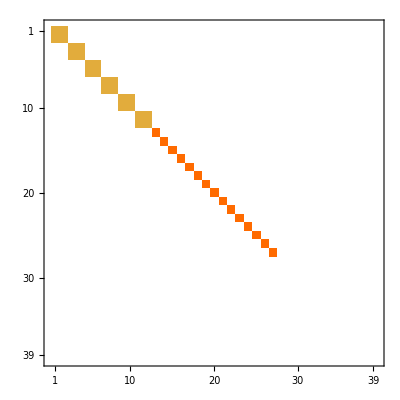

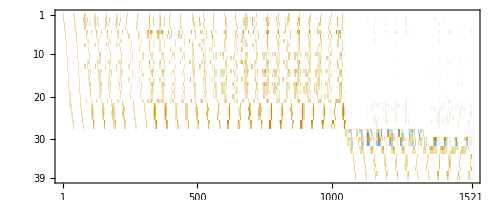

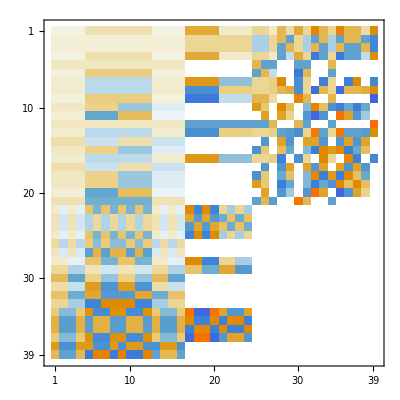

```mathematica
z//MatrixPlot
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=Conjugate[s] . ReplacePart[z,Thread[nz->X]] . s  //Flatten;
A=CoefficientArrays[Thread[m==0],X][[2]]//Simplify//Normal;
a=(A[[#,All]]&/@(Flatten[FirstPosition[#,1]&/@ RowReduce[Transpose[Chop[N[A]]]]]) )//FullSimplify;
Transpose[N[A]]//RowReduce//MatrixPlot
a//MatrixPlot
```

```mathematica
Organize[e_]:=Module[{l,r,L},
l=e[[1]];
r=e[[2]];
L=LCM@@(Level[List@@#,1]&/@Flatten[{l,r}]//Flatten//Denominator);
e[[0]][(l-r)//ExpandAll,0]
];
b=Inverse[N[a]]//Chop;
b=RootApproximant/@b;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->Simplify[b.X]]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
mx=(Min [Cases[eqn, (a_. * #)>= 0 :>a]])^-1&/@X;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->Simplify[b.(mx*X)]]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
eqn=Organize/@eqn;
eqn//MatrixForm; 
B=Table[Coefficient[eqn[[i]][[1]],X],{i,Length[eqn]}];
B//MatrixPlot;
```

```mathematica
<<math4ti2`
basis =zsolve[#>=0&/@Flatten[B.X]][[2]];
basis//MatrixForm
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
d=b. (mx*#) &/@basis //FullSimplify;
d=Sort[d,#1[[1]] <= #2[[1]]&];
d//Transpose//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(2 (5+√5))+ | √(2 (5+√5))+ | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) |  | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | -2 (3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) |  | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) |  | √(3-√5) |  | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | (-3+√5)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) |  | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 |  | √(3-√5) |  | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | (-3+√5)/(√2) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 |  | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) |  | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FindRowProducts[M_,N_]:=Module[
{m=Length[M],n=Length[N], results={}},
Do[
With[{product=M[[i]]*N[[j]]//Chop},
If[MemberQ[N,product],
AppendTo[results,{i,j,Position[N,product]//Flatten}]]
],{i,1,m},{j,1,n}];
results
]
FusionCandidates=FindRowProducts[d[[;;5,;;24]],d[[All,;;24]]//N//Chop];
FusionCandidates//Length
FusionCandidates//MatrixForm
```

151

(1 | 1 | {1,2}
1 | 2 | {1,2}
1 | 3 | {3}
1 | 4 | {4}
1 | 5 | {5}
1 | 6 | {6,7}
1 | 7 | {6,7}
1 | 8 | {8}
1 | 9 | {9,12}
1 | 10 | {10,11}
1 | 11 | {10,11}
1 | 12 | {9,12}
1 | 13 | {13}
1 | 14 | {14}
1 | 15 | {15}
1 | 16 | {16,17,18,19}
1 | 17 | {16,17,18,19}
1 | 18 | {16,17,18,19}
1 | 19 | {16,17,18,19}
1 | 20 | {20}
1 | 21 | {21,22}
1 | 22 | {21,22}
1 | 23 | {23}
1 | 24 | {24}
1 | 25 | {25,26}
1 | 26 | {25,26}
1 | 27 | {27}
1 | 28 | {28}
1 | 29 | {29}
1 | 30 | {30}
1 | 31 | {31}
1 | 32 | {32}
1 | 33 | {33}
1 | 34 | {34}
1 | 35 | {35}
1 | 36 | {36}
1 | 37 | {37}
1 | 38 | {38}
1 | 39 | {39}
2 | 1 | {1,2}
2 | 2 | {1,2}
2 | 3 | {3}
2 | 4 | {4}
2 | 5 | {5}
2 | 6 | {6,7}
2 | 7 | {6,7}
2 | 8 | {8}
2 | 9 | {9,12}
2 | 10 | {10,11}
2 | 11 | {10,11}
2 | 12 | {9,12}
2 | 13 | {13}
2 | 14 | {14}
2 | 15 | {15}
2 | 16 | {16,17,18,19}
2 | 17 | {16,17,18,19}
2 | 18 | {16,17,18,19}
2 | 19 | {16,17,18,19}
2 | 20 | {20}
2 | 21 | {21,22}
2 | 22 | {21,22}
2 | 23 | {23}
2 | 24 | {24}
2 | 25 | {25,26}
2 | 26 | {25,26}
2 | 27 | {27}
2 | 28 | {28}
2 | 29 | {29}
2 | 30 | {30}
2 | 31 | {31}
2 | 32 | {32}
2 | 33 | {33}
2 | 34 | {34}
2 | 35 | {35}
2 | 36 | {36}
2 | 37 | {37}
2 | 38 | {38}
2 | 39 | {39}
3 | 1 | {3}
3 | 2 | {3}
3 | 3 | {1,2}
3 | 4 | {5}
3 | 5 | {4}
3 | 6 | {6,7}
3 | 7 | {6,7}
3 | 8 | {8}
3 | 9 | {10,11}
3 | 10 | {9,12}
3 | 11 | {9,12}
3 | 12 | {10,11}
3 | 13 | {14}
3 | 14 | {13}
3 | 15 | {15}
3 | 16 | {16,17,18,19}
3 | 17 | {16,17,18,19}
3 | 18 | {16,17,18,19}
3 | 19 | {16,17,18,19}
3 | 20 | {20}
3 | 21 | {23}
3 | 22 | {23}
3 | 23 | {21,22}
3 | 24 | {24}
3 | 25 | {25,26}
3 | 26 | {25,26}
3 | 27 | {28}
3 | 28 | {27}
3 | 29 | {30}
3 | 30 | {29}
3 | 31 | {31}
3 | 32 | {32}
3 | 33 | {33}
3 | 36 | {37}
3 | 37 | {36}
3 | 38 | {38}
3 | 39 | {39}
4 | 1 | {4}
4 | 2 | {4}
4 | 3 | {5}
4 | 4 | {1,2}
4 | 5 | {3}
4 | 6 | {8}
4 | 7 | {8}
4 | 8 | {6,7}
4 | 9 | {13}
4 | 10 | {14}
4 | 11 | {14}
4 | 12 | {13}
4 | 13 | {9,12}
4 | 14 | {10,11}
4 | 32 | {33}
4 | 33 | {32}
4 | 38 | {39}
4 | 39 | {38}
5 | 1 | {5}
5 | 2 | {5}
5 | 3 | {4}
5 | 4 | {3}
5 | 5 | {1,2}
5 | 6 | {8}
5 | 7 | {8}
5 | 8 | {6,7}
5 | 9 | {14}
5 | 10 | {13}
5 | 11 | {13}
5 | 12 | {14}
5 | 13 | {10,11}
5 | 14 | {9,12}
5 | 32 | {33}
5 | 33 | {32}
5 | 38 | {39}
5 | 39 | {38})

## Describing Invertible Defects

```mathematica
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=Which[MatrixQ[#[[1]]]&&MatrixQ[#[[2]]],#[[1]].#[[2]], (!MatrixQ[#[[1]]])||(!MatrixQ[#[[2]]]),#[[1]]*#[[2]]]&/@Transpose[{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]
tr[x_]:=Which[MatrixQ[x],Tr[x],!MatrixQ[x],x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],!MatrixQ[x],1/x];
threshold=24;
di=Select[d,#[[1]]==1&];
dn=Select[d,#[[1]]!=1&];
Y=Array[y,{Length[d]-threshold,3}];
YY=Y//Flatten;
Z=Array[yz,{Length[d]-threshold,3}];
ZZ=Z//Flatten;
P=Array[pp,{Length[d]-threshold,4}];
PP=P//Flatten;
LP=Array[Which[#<=threshold,1,#>threshold,
{{P[[#-threshold,1]] ,P[[#-threshold,2]] },{P[[#-threshold,3]],P[[#-threshold,4]]}}]&,Length[d]];
LPi=inv/@LP//Simplify;
l[i_,v_:Y]:=Array[Which[#<=threshold,d[[i,#]],#>threshold,
{{v[[#-threshold,1]] ,v[[#-threshold,2]] },{v[[#-threshold,3]],d[[i,#]]-v[[#-threshold,1]]}}]&,Length[d]];
```

```mathematica
FindIntegerCombinations[M_,v_]:=Module[{n=Length[M],m=Length[v],MT,ubounds,results={}},
MT=Transpose[N[M]];
ubounds=Table[Module[{sol},
sol=LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]],{i,n}];
enumerate[rem_,idx_,current_]:=Which[idx>n,If[rem==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results]
```

```mathematica
ii={{1,0},{0,1}};
aa={{1,0},{0,-1}};
bb={{0,1},{1,0}};
cc={{0,1},{-1,0}};
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii,ii};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa,aa};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,aa,aa,aa,cc,cc,aa,aa,cc,cc,aa,cc,cc,cc,cc,-aa};
Di={L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗(Lχ⊗Lχ),Lχ,Lχ⊗(Lχ⊗Lχ)};
fam[x_]:=Which[MemberQ[{3,4},x],3,MemberQ[{5,6},x],4,MemberQ[{7,8},x],5,True,x];
MatrixForm[MatrixForm/@#]&/@Di
ConjugateQ[a_,b_]:=MemberQ[N[(#⊗a)⊗#]&/@Di,b];
```

{(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)),(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(1 | 0
0 | 1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(-1 | 0
0 | -1)
(1 | 0
0 | 1)),(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
-1
-1
-1
-1
-1
-1
-1
-1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(1 | 0
0 | 1)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(0 | -1
-1 | 0)
(-1 | 0
0 | -1)),(1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
1
-1
-1
-1
-1
-1
-1
-1
-1
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(1 | 0
0 | 1)
(1 | 0
0 | 1)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(1 | 0
0 | 1)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(0 | 1
1 | 0)
(-1 | 0
0 | -1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(1 | 0
0 | -1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(-1 | 0
0 | 1)
(1 | 0
0 | -1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
-1
1
1
-1
-1
1
1
-1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(1 | 0
0 | -1)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(0 | 1
-1 | 0)
(-1 | 0
0 | 1)),(1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
1
-1
-1
1
-1
1
1
-1
-1
1
1
-1
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(1 | 0
0 | -1)
(1 | 0
0 | -1)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(1 | 0
0 | -1)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(0 | -1
1 | 0)
(-1 | 0
0 | 1))}

```mathematica
Reduce[And@@Thread[Flatten[(LP⊗# -#⊗LP)&/@Di]==0],PP,Complexes,Backsubstitution->True]
```

pp[1,2]==0&&pp[1,3]==0&&pp[2,2]==0&&pp[2,3]==0&&pp[3,2]==0&&pp[3,3]==0&&pp[4,2]==0&&pp[4,3]==0&&pp[4,4]==pp[4,1]&&pp[5,2]==0&&pp[5,3]==0&&pp[5,4]==pp[5,1]&&pp[6,2]==0&&pp[6,3]==0&&pp[7,2]==0&&pp[7,3]==0&&pp[8,2]==0&&pp[8,3]==0&&pp[8,4]==pp[8,1]&&pp[9,2]==0&&pp[9,3]==0&&pp[9,4]==pp[9,1]&&pp[10,2]==0&&pp[10,3]==0&&pp[11,2]==0&&pp[11,3]==0&&pp[11,4]==pp[11,1]&&pp[12,2]==0&&pp[12,3]==0&&pp[12,4]==pp[12,1]&&pp[13,2]==0&&pp[13,3]==0&&pp[13,4]==pp[13,1]&&pp[14,2]==0&&pp[14,3]==0&&pp[14,4]==pp[14,1]&&pp[15,2]==0&&pp[15,3]==0

```mathematica
Family=6;
FusionCandidates={tr/@(Di[[#[[1]]]]⊗l[#[[2]]]⊗Di[[#[[3]]]])//Simplify,FindIntegerCombinations[d[[All,;;threshold]],d[[fam[#[[1]]],;;threshold]]d[[#[[2]],;;threshold]]d[[fam[#[[3]]],;;threshold]]]}&/@Tuples[{Range@Length@Di,{Family},{1}}];
FusionCandidates=FusionCandidates~Join~({tr/@(l[#[[1]]]⊗l[#[[2]]])//Simplify,FindIntegerCombinations[d[[All,;;threshold]],d[[#[[1]],;;threshold]]d[[#[[2]],;;threshold]]]}&/@Tuples[{{Family},{Family}}]);
FusionCandidates=DeleteDuplicates[FusionCandidates];
fusions=Transpose[{FusionCandidates[[All,1]], #.d&/@#}]&/@Tuples[FusionCandidates[[All,2]]];
fusions=Thread[#[[1]]==#[[2]]]&/@Transpose[#]&/@#&/@fusions;
fusions=DeleteDuplicates[fusions];
```

```mathematica
solns=Solve[And @@(Flatten[#]),YY ]&/@fusions//Simplify;
mask =(#!={})&/@solns;
defects=Pick[(Simplify[l[Family]/.#][[1]])&/@solns,mask];
rules=Pick[Tuples[FusionCandidates[[All,2]]],mask];
MatrixForm[MatrixForm/@#]&/@defects
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

{(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | y[1,2]
2/y[1,2] | 0)
(√2 | 0
y[2,3] | √2)
(0 | y[3,2]
2/y[3,2] | 0)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(0 | y[6,2]
2/y[6,2] | 0)
(-√2 | 0
y[7,3] | -√2)
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | y[10,2]
2/y[10,2] | 0)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | 0
y[15,3] | 0)),(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | y[1,2]
2/y[1,2] | 0)
(√2 | 0
y[2,3] | √2)
(0 | y[3,2]
2/y[3,2] | 0)
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(0 | y[6,2]
2/y[6,2] | 0)
(-√2 | 0
y[7,3] | -√2)
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(0 | y[10,2]
2/y[10,2] | 0)
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(0 | 0
y[15,3] | 0))}

```mathematica
prod=tr/@(defects[[1]]⊗(defects[[1]]/.Thread[YY->ZZ]));
Reduce[(And@@Thread[prod==#.d]),Flatten[{YY,ZZ}],Complexes, Backsubstitution->True]&/@FindIntegerCombinations[Transpose@Pick[Transpose[d],FreeQ[#,_Symbol]&/@prod],Pick[prod,FreeQ[#,_Symbol]&/@prod]]
```

{y[1,2]≠0&&y[3,2]≠0&&y[6,2]≠0&&y[10,2]≠0&&yz[1,2]==y[1,2]&&yz[3,2]==y[3,2]&&yz[6,2]==y[6,2]&&yz[10,2]==y[10,2]}

```mathematica
MatrixForm/@rules
```

{(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}